```mathematica
(*在Mathematica与大学物理计算p28，给出了如下的阻尼摆计算代码与相图*)
Clear[g,L,Ω,v0,ω0,η,tm,s,θ]
g=9.8;L=1.5;Ω=√(g/L);
v0=0.2;ω0=v0/L;η=0.1;tm=80;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]]-η*θ'[t],θ[0]==0,θ'[0]==ω0},θ,{t,0,tm}];
θ=θ/.s[[1]];
Plot[θ[t],{t,0,tm},PlotRange->{-0.06,0.06},PlotStyle->Thickness[0.004],AxesStyle->Thickness[0.003]]
ParametricPlot[{θ[t],θ'[t]},{t,0,tm},PlotRange->{{-0.06,0.06},{-0.15,0.15}},AxesLabel->{"θ","θ'"},AspectRatio->1,PlotStyle->Thickness[0.004],AxesStyle->Thickness[0.003]]
```

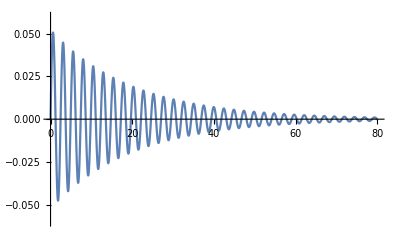

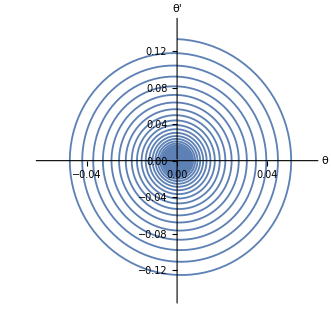

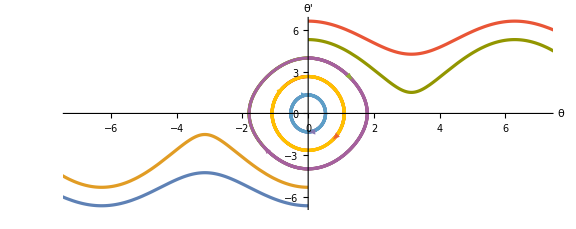

```mathematica
(*在上面的这张以θ为横坐标，θ'为纵坐标的相图上，每一个点都代表这个力学系统的一个确定的状态，而且这个点之后的轨迹也是完全确定的。这样，我们就可以通过一张相图看出这个力学系统所有的状态。在下面，我画出了更加完整的单摆的相图，对应着多种不同的初始条件*)
Clear["Global`*"]
g=9.8;L=1.5;Ω=√(g/L);tm=5;
a=0;
sol=ParametricNDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==a,θ'[0]==v0/L},{θ,θ'},{t,0,tm},{v0}];
ParametricPlot[Evaluate[Table[{θ[v0][t],θ[v0]'[t]}/.sol,{v0,-10,10,2}]],{t,0,tm},AxesLabel->{"θ","θ'"},AspectRatio->0.4,PlotStyle->Thickness[0.004],AxesStyle->Thickness[0.003],ImageSize->Large]/.Line->({Arrowheads[{0,.04,0}],Arrow[#]}&)
```

```mathematica
问题
1.解释单摆相图不同的曲线代表的运动状态
2.这个相图实际上并不是我们平常见到的单摆相图，问题是这张图中的θ是没有周期的。如何将θ的周期性表现出来呢（可以百度一下单摆相图）
3.参考上面的代码，画出阻尼摆的相图并解释
```

```mathematica
作者：高家鹏
```